```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
data=RandomVariate[WeibullDistribution[2,500],100];
```

```mathematica
m=Median[data];
m=100;
```

```mathematica
censor=Map[(#>m)&,data];
```

```mathematica
data1=Map[(If[#>m,m,#])&,data];
```

```mathematica
U[α_,β_]=Simplify[Total[Map[(PowerExpand[-Log[Simplify[If[#==m,1-CDF[WeibullDistribution[α,β],x],PDF[WeibullDistribution[α,β],x]],x>0]]]/.x->#)&,data1]]];
dU[x_,y_]=Simplify[GradientG[U[x,y],{x,y}]];
ddU[x_,y_]=Simplify[HessianH[U[x,y],{x,y}]];
CHAINS=3;
STEPS=10;
outbnd[q_]:=AnyTrue[q,(#<=0||#>1000)&];
qinit=RandomVariate[UniformDistribution[],{CHAINS,2}];
```

```mathematica
mle=FindMinimum[{U[α,β],α>0&&β>0},{α,β}]
```

{25.8993,{α→3.16323,β→301.35}}

```mathematica
sd=Diagonal[Sqrt[Inverse[ddU[α,β]/.Last[mle]]]]
```

{1.81786,199.282}

```mathematica
INTERVAL=1001;
QS=hmc[U,dU,ddU,2,5000,10000,True,True,qinit];
```

100125988.41.401010.5241930.50175278.696226067.1212276.0.001667450.00137806True{1,11}{1,2,11}

20025584.1616394.70.8482130.26290379.95821482.935664.120.006332150.00475744False{1,11}{1,11}

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{723195.,-0.164611},{-0.164611,5.76701×10^-7}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

3003603.2462.279320.61620.5343680.9068684.1531482.510.009270910.0084281True{1,11}{1,11}

400475.77484276.060.2136970.37013579.3798419.002155.1550.007661910.0290961False{1,9}{1,11}

50051130.337.400320.7790540.3826980.57971210.9189.10230.004324950.147065True{2,8,11}{1,11}

60066.138121650.310.7661130.40510482.96421210.9189.10230.004324950.147065False{2,8,11}{1,11}

70071132.383.293380.3657530.55068878.5321210.9189.10230.004324950.147065True{2,8,11}{1,11}

80087.501816027.370.6666670.5773581.60051210.9189.10230.004324950.147065False{2,8,11}{1,11}

90091131.924.258750.3926530.065478.99051210.9189.10230.004324950.147065True{2,8,11}{1,11}

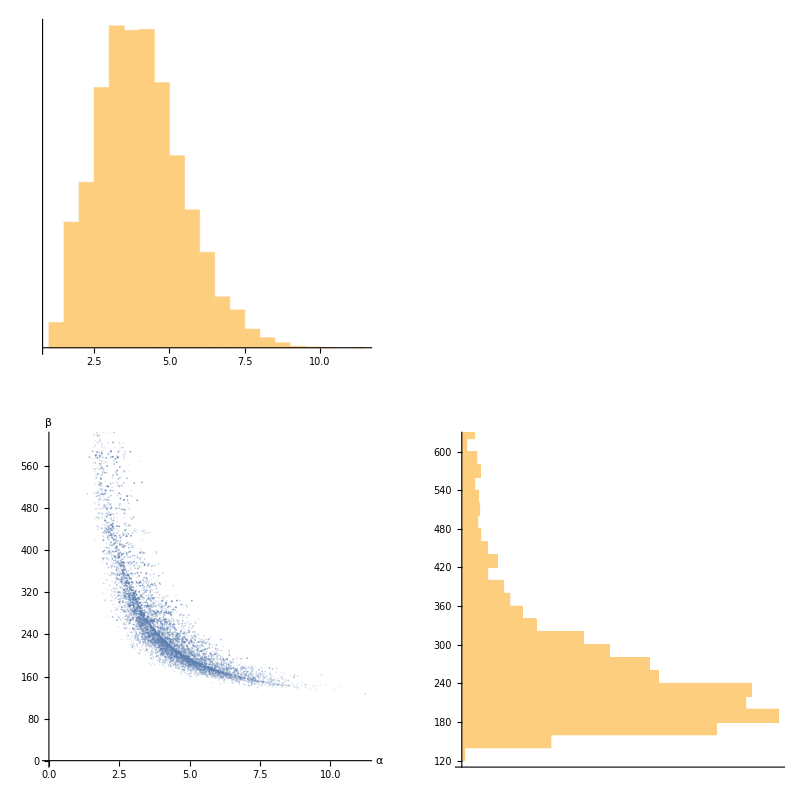

```mathematica
GraphicsGrid[{{Histogram[QS[[;;,1]],Automatic,"Probability",Ticks->{Automatic,None},AspectRatio->.5]},{ListPlot[QS,PlotStyle->Opacity[.2],AspectRatio->1,AxesLabel->{α,β}],Histogram[QS[[;;,2]],Automatic,"Probability",BarOrigin->Left,AspectRatio->2,Ticks->{None,Automatic}]}}]
```

```mathematica
Mean[QS]
```

{4.04203,285.058}

```mathematica
StandardDeviation[QS]
```

{1.41357,142.579}

```mathematica
Quantile[QS,{.025,.5,.975}]//MatrixForm
```

(1.67201 | 3.94024 | 7.19956
156.414 | 238.604 | 742.468)

```mathematica
Mean[WeibullDistribution[2,500]]//N
```

443.113

```mathematica
FindMinimum[{U[x,y],x>0&&y>0},{x,y}]
```

{25.8993,{x→3.16323,y→301.35}}

```mathematica
Export["weibull-censored.csv",QS]
```

weibull-censored.csv

```mathematica
psrf[QS]
```

{1.00118,1.00085}

```mathematica
r = Exp[-(100/QS[[;;,2]])^QS[[;;,1]]];
```

```mathematica
Quantile[r,{.025,.5,.975}]
```

{0.932083,0.964537,0.989605}

```mathematica
Exp[-(100/500)^2]//N
```

0.960789

```mathematica
α Exp[-InverseCDF[NormalDistribution[],.975] sd[[1]]/α]/.Last[mle]
```

1.02555

```mathematica
α Exp[InverseCDF[NormalDistribution[],.975] sd[[1]]/α]/.Last[mle]
```

9.75672

```mathematica
β Exp[-InverseCDF[NormalDistribution[],.975] sd[[2]]/β]/.Last[mle]
```

82.4465

```mathematica
β Exp[InverseCDF[NormalDistribution[],.975] sd[[2]]/β]/.Last[mle]
```

1101.46